Exercises for Section 16 | Real-World Data

Find the flag of Switzerland. |

EXPECTED OUTPUT »

-Graphics- | ×

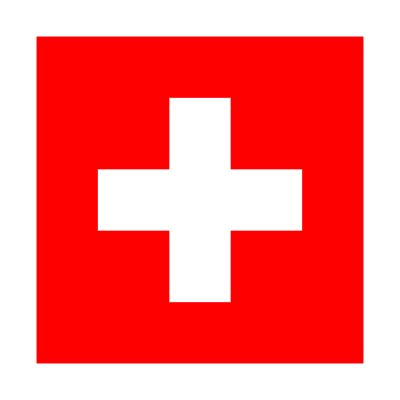

"Graphics[{Thickness[0.00125], {FaceForm[{RGBColor[1., 0., 0.], Opacity[1.]}], \n   FilledCurve[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}}}, \n    {{{0., 0.}, {0., 800.}, {800., 800.}, {800., 0.}}}]}, \n  {FaceForm[{RGBColor[1., 1., 1.], Opacity[1.]}], \n   FilledCurve[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}}}, \n    {{{150., 475.}, {650., 475.}, {650., 325.}, {150., 325.}}}], \n   FilledCurve[{{{0, 2, 0}, {0, 1, 0}, {0, 1, 0}}}, \n    {{{325., 650.}, {475., 650.}, {475., 150.}, {325., 150.}}}]}}, \n {ImageSize -> {{128}, {85}}, AspectRatio -> Automatic, ImageSize -> {338., 338.}, \n  PlotRange -> {{0., 800.}, {0., 800.}}}]"

```mathematica
LinguisticAssistant
InputForm[Entity["Country","Switzerland"][EntityProperty["Country","Flag"]]]
```

Get an image of an elephant. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Entity["Species","Family:Elephantidae"][EntityProperty["Species","Image"]]
```

-Graphics-

Use the "Mass" property to generate a list of the masses of the planets. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
EntityClass["Planet",All]["Mass"]
EntityValue[EntityClass["Planet",All],"Mass"]
```

{3.3×10^23 kg,4.867×10^24 kg,5.97×10^24 kg,6.417×10^23 kg,1.898×10^27 kg,5.683×10^26 kg,8.681×10^25 kg,1.024×10^26 kg}

{3.3×10^23 kg,4.867×10^24 kg,5.97×10^24 kg,6.417×10^23 kg,1.898×10^27 kg,5.683×10^26 kg,8.681×10^25 kg,1.024×10^26 kg}

Make a bar chart of the masses of the planets. |

EXPECTED OUTPUT »

-Graphics- | ×

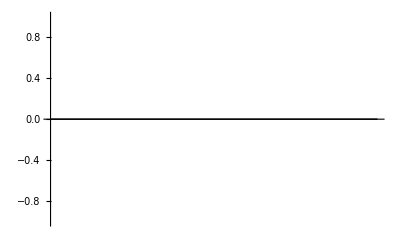

```mathematica
BarChart[EntityValue[EntityClass["Planet",All],"Mass"]]
```

Make an image collage of images of the planets. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ImageCollage[EntityValue[EntityClass["Planet",All],"Image"]]
```

-Graphics-

Edge detect the flag of China. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
EdgeDetect[Entity["Country","China"][EntityProperty["Country","Flag"]]]
```

-Graphics-

Find the height of the Empire State Building. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Entity["Building","EmpireStateBuilding::h583b"][EntityProperty["Building","Height"]]
```

1250. ft

Compute the height of the Empire State Building divided by the height of the Great Pyramid. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Quantity[1250, "Feet"]/Entity["Building","GreatPyramidOfGiza::jbm66"][EntityProperty["Building","Height"]]
```

2.74101

Compute the elevation of Mount Everest divided by the height of the Empire State Building. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Entity["Mountain","MountEverest"][EntityProperty["Mountain","Elevation"]]/Quantity[1250, "Feet"]
```

23.2254

Find the dominant colors in the painting The Starry Night. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
DominantColors[EntityValue[Entity["Artwork","TheStarryNight::VincentVanGogh"],"Image"]]
```

{RGBColor[0.3332092589900391, 0.4351871320758253, 0.6023091749044202],RGBColor[0.14034730566124173, 0.1488087163233582, 0.1328080803391138],RGBColor[0.4972570418496233, 0.5560647169382823, 0.5124423328359278],RGBColor[0.7205758097128038, 0.6443860782139894, 0.1551868324905521]}

Find the dominant colors in an image collage of the flag images of all countries in Europe. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
DominantColors[ImageCollage[EntityValue[EntityClass["Country","Europe"][EntityProperty["Country","Flag"]],"Image"]]];
Entity["GeographicRegion","Europe"][EntityProperty["GeographicRegion","Countries"]]
```

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

ImageCollage::invarg: "\"Hold[EntityFramework`BatchMapBy[<<46>>ue[<<2>>] & , <<2>>]]\"" should be a list of images, a list of rules weight -> image, or a rule weights -> images.

DominantColors::imginv: Expecting an image or graphics instead of "\"{ImageCollage[Hold[EntityFramework`BatchMapBy[<<3>>]]]}\"".

{Albania,Andorra,Austria,Belarus,Belgium,Bosnia and Herzegovina,Bulgaria,Croatia,Czech Republic,Denmark,Estonia,Faroe Islands,Finland,France,Germany,Gibraltar,Greece,Guernsey,Hungary,Iceland,Ireland,Isle of Man,Italy,Jersey,Kosovo,Latvia,Liechtenstein,Lithuania,Luxembourg,North Macedonia,Malta,Moldova,Monaco,Montenegro,Netherlands,Norway,Poland,Portugal,Romania,Russia,San Marino,Serbia,Slovakia,Slovenia,Spain,Svalbard,Sweden,Switzerland,Ukraine,United Kingdom,Vatican City}

```mathematica
DominantColors[ImageCollage[EntityValue[Entity["GeographicRegion","Europe"][EntityProperty["GeographicRegion","Countries"]],"FlagImage"]]]
DominantColors[ ImageCollage[EntityValue[EntityClass["Country", "Europe"], "FlagImage"]]]
```

{RGBColor[0.8235515900854293, 0.07670421643221803, 0.11274925171259464],RGBColor[0.9985673544543981, 0.9977766939783458, 0.9980916216812022],RGBColor[0.10443943519452609, 0.2958107669812863, 0.5966210706196059],RGBColor[0.9955325070268238, 0.806199044498479, 0.019339031613829712],RGBColor[0.004715991737305436, 0.15233086176224436, 0.5380029395760613],RGBColor[0.9572753194538116, 0.011044694948405378, 0.009669565266252306],RGBColor[0.26523220886446774, 0.6761319487734694, 0.8833022549956586],RGBColor[0.0015826756900012135, 0.5869383129238022, 0.2772207255414853],RGBColor[0.0017478787641514652, 3.465780645364624*^-4, 2.2763911285046638*^-4],RGBColor[0.008805255888973174, 0.4716079695616871, 0.2919613989913124],RGBColor[0.6190836027187422, 0.1866105875525206, 0.22130206797934293],RGBColor[0.05210719839921584, 0.09136826579527857, 0.6194767531150712],RGBColor[0.0015662273370502895, 0.3998781983289395, 5.0452437732334684*^-5],RGBColor[0.8177151139437947, 0.6527399205115243, 0.2488653499844407],RGBColor[0.9893345180171568, 0.464891958189744, 0.0032624343642381217]}

{RGBColor[0.8183433501428342, 0.08121649529200531, 0.12643582422603533],RGBColor[0.9982488132746107, 0.9976057947283211, 0.9980440959481481],RGBColor[0.09042044025343923, 0.2631426510561981, 0.6330412843878602],RGBColor[0.9946609030060517, 0.8230886382964921, 0.06267544137095424],RGBColor[0.022032342661544742, 0.1267484311307489, 0.5870582485554472],RGBColor[0.2654746610743897, 0.6767624463903962, 0.8834859446363911],RGBColor[0.0015866306541914678, 0.5869158128030737, 0.2772509824239156],RGBColor[0.0018773493958880736, 2.6329405796014733*^-4, 2.281340902976298*^-4],RGBColor[0.003219559823204549, 0.4703709252493747, 0.2912846591847063],RGBColor[0.6205926405641301, 0.18941356346136118, 0.2246154595530363],RGBColor[0.8148631409166119, 0.6518194980253419, 0.2521862549069703],RGBColor[0.005642512533245828, 0.398803699663992, 1.199889714314091*^-4],RGBColor[0.9902508202555852, 0.47186026717245094, 0.002778393649879522]}

```mathematica
DominantColors[ImageCollage[EntityValue[EntityClass["Country","Europe"],"FlagImage"]]]
```

{RGBColor[0.8183433501428342, 0.08121649529200531, 0.12643582422603533],RGBColor[0.9982488132746107, 0.9976057947283211, 0.9980440959481481],RGBColor[0.09042044025343923, 0.2631426510561981, 0.6330412843878602],RGBColor[0.9946609030060517, 0.8230886382964921, 0.06267544137095424],RGBColor[0.022032342661544742, 0.1267484311307489, 0.5870582485554472],RGBColor[0.2654746610743897, 0.6767624463903962, 0.8834859446363911],RGBColor[0.0015866306541914678, 0.5869158128030737, 0.2772509824239156],RGBColor[0.0018773493958880736, 2.6329405796014733*^-4, 2.281340902976298*^-4],RGBColor[0.003219559823204549, 0.4703709252493747, 0.2912846591847063],RGBColor[0.6205926405641301, 0.18941356346136118, 0.2246154595530363],RGBColor[0.8148631409166119, 0.6518194980253419, 0.2521862549069703],RGBColor[0.005642512533245828, 0.398803699663992, 1.199889714314091*^-4],RGBColor[0.9902508202555852, 0.47186026717245094, 0.002778393649879522]}

Make a pie chart of the GDP of countries in Europe. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
PieChart[EntityValue[EntityClass["Country","Europe"],"GDP"]]
```

-Graphics-

Add an image of a koala to an image of the Australian flag. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ImageAdd[Entity["Species","Species:PhascolarctosCinereus"][EntityProperty["Species","Image"]],Entity["Country","Australia"][EntityProperty["Country","Flag"]]]
```

-Graphics-

Make an image collage of the flags of all countries in Europe, using the "FlagImage" property. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ImageCollage[EntityValue[EntityClass["Country","Europe"],"FlagImage"]]
```

-Graphics-

Edge detect an image of the painting The Starry Night. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
EdgeDetect[EntityValue[Entity["Artwork","TheStarryNight::VincentVanGogh"],"Image"]]
```

-Graphics-

Color negate the Mona Lisa painting. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ColorNegate[EntityValue[Entity["Artwork","MonaLisa::LeonardoDaVinci"],"Image"]]
```

-Graphics-